## RQ decomposition

I want to do a QR backwards for practice.  I am going to rewrite the code from 4610/5627

```mathematica
MyQR[AIn_]:= Module[{A=AIn,m,n,v,V},
{m,n}=Dimensions[A];
V=ConstantArray[0,{m,n}];
(* Householder Reduction from Script Version 3 *)
Do[
v=A⟦i;;-1,i⟧;
v⟦1⟧-=Norm[v]; v=v/Norm[v];
V⟦i;;-1,i⟧=v;
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n-1}];
(* Returns Householder vectors in V *)
{Chop[A],V}
]
```

To do it the other way around I need to first make sure I understand how to zero the bottom row of of a short fat matrix with a householder

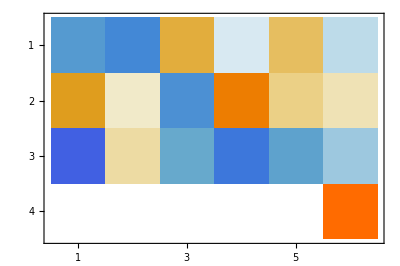
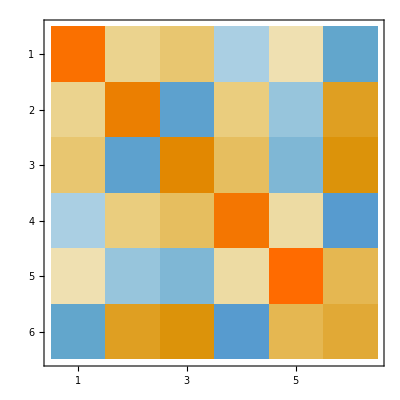
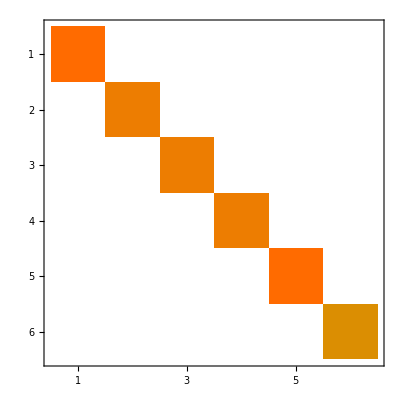
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

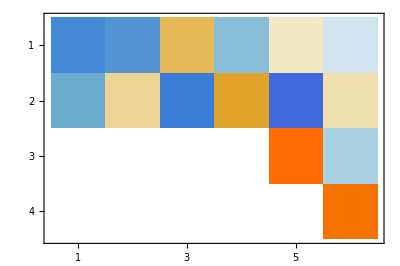
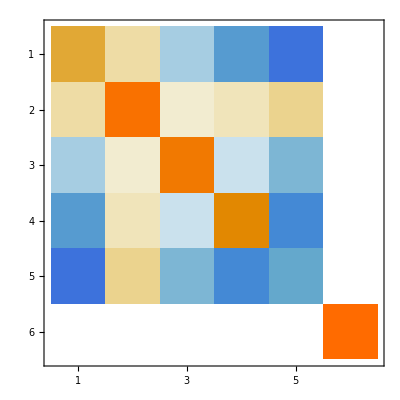
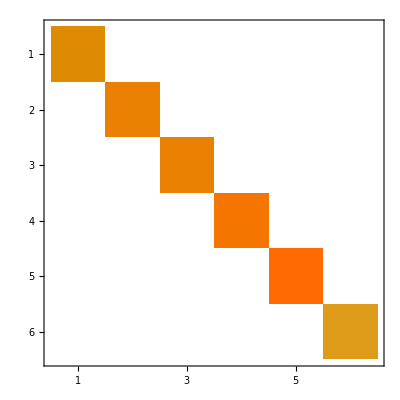
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

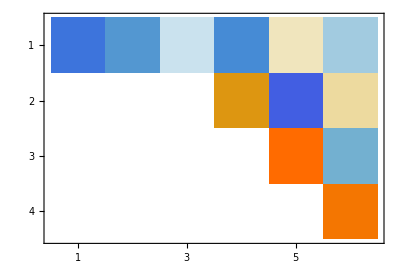
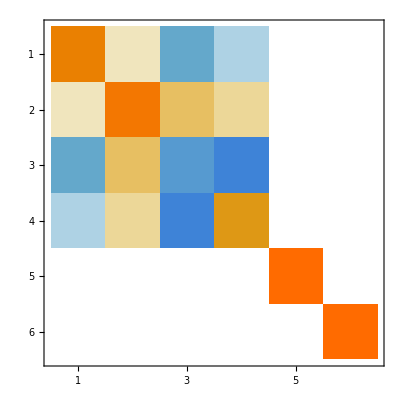
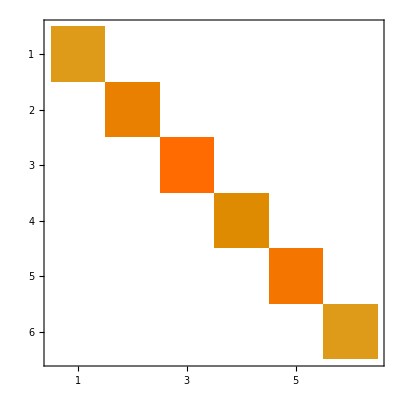
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

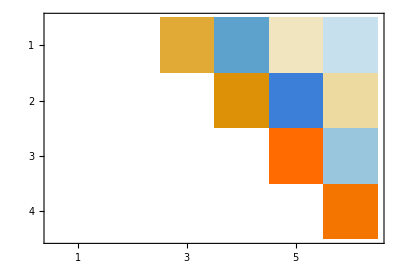
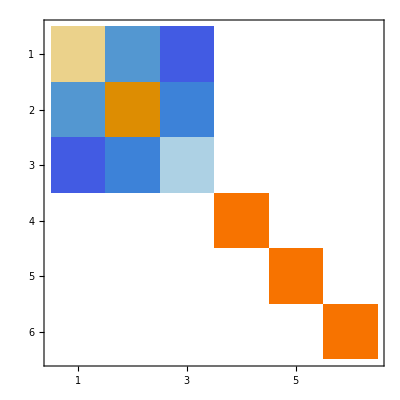
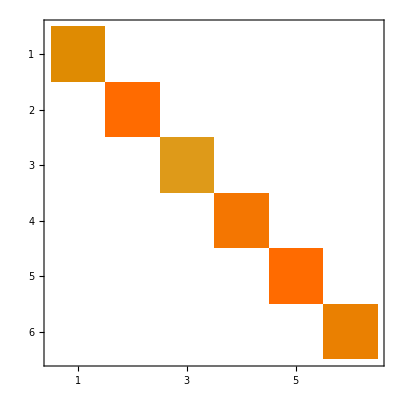
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
R=A;Q=IdentityMatrix[n];

v=R⟦m,All⟧; v⟦n⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-1,All⟧; v⟦n-0;;n⟧*=0;v⟦-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-2,All⟧; v⟦n-1;;n⟧*=0;v⟦n-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]

v=R⟦m-3,All⟧; v⟦n-2;;n⟧*=0;v⟦n-3⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]
```

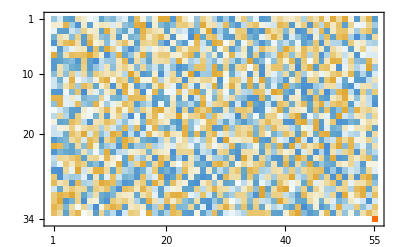
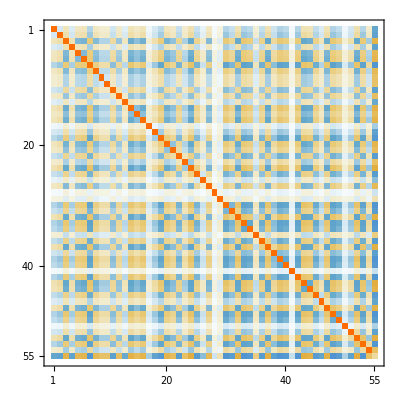
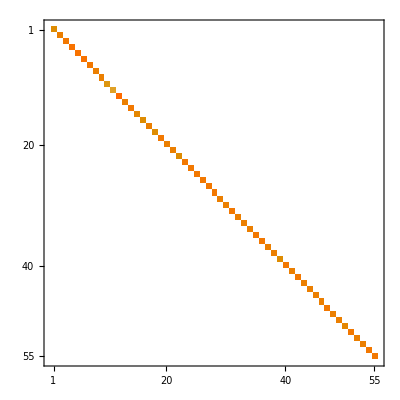
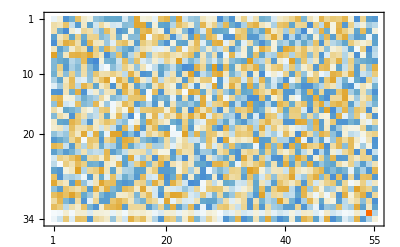
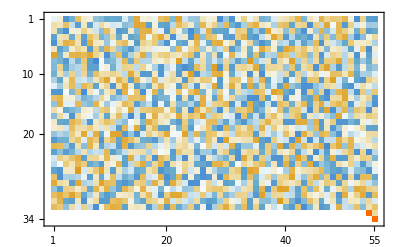
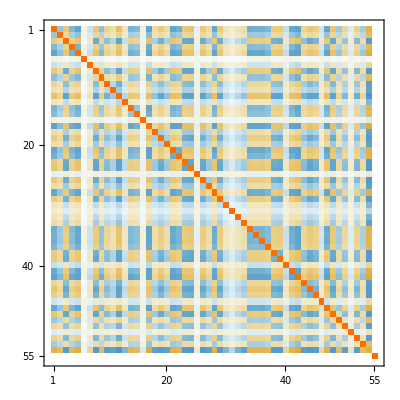
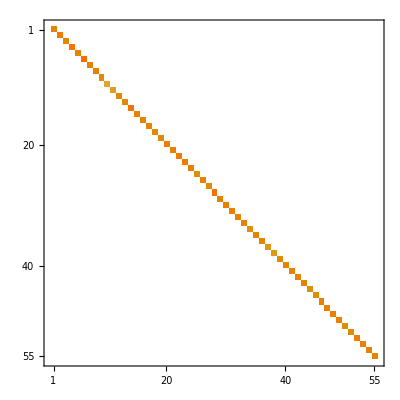
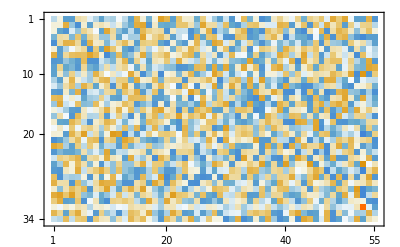
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{m,n}={34,55};
A=RandomReal[{-1,1},{m,n}];
R=A;Q=IdentityMatrix[n];

Table[
v=R⟦m-i,All⟧; v⟦n+1-i;;n⟧*=0;v⟦n-i⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{A.H,R,H,Qᵀ.Q}]],
{i,0,m-1}]
```

```mathematica
v=R⟦m,All⟧; v⟦n⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-1,All⟧; v⟦n-0;;n⟧*=0;v⟦-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-2,All⟧; v⟦n-1;;n⟧*=0;v⟦n-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]

v=R⟦m-3,All⟧; v⟦n-2;;n⟧*=0;v⟦n-3⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

«1 more identical outputs»

```mathematica
MyRQ[AIn_]:= Module[{A=AIn,m,n,v,V},
{m,n}=Dimensions[A];
V=ConstantArray[0,{m,n}];
(* Householder Reduction from Script Version 3 *)
Do[
v=A⟦1;;i,i⟧;
v⟦-11⟧-=Norm[v]; v=v/Norm[v];
V⟦i;;1,i⟧=v;
Do[
A⟦1;;i,j⟧=A⟦1;;i,j⟧-2 v (v.A⟦1;;i,j⟧),
{j,i,n}],
{i,n,2,-1}];
(* Returns Householder vectors in V *)
{Chop[A],V}
]
```

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{R1,V1}=MyQR[A];
{R2,V2}=MyRQ[A];
Map[SingularValueList,{A,R}]
MatrixPlot[R]
```

Set::take: Cannot take positions 12 through 1 in {{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},«2»}.

Set::take: Cannot take positions 11 through 1 in {{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},«2»}.

Part::partw: Part -11 of {0.883944,-0.965514,0.178854,0.525925,-0.746343,-0.868076,-0.495938,0.15082,0.443691,-0.586411} does not exist.

Set::take: Cannot take positions 10 through 1 in {{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},{0,0,0,0,0,0,0,0,0,0,«2»},«2»}.

General::stop: Further output of Set::take will be suppressed during this calculation.

Part::partw: Part -11 of {0.883944,-0.965514,0.178854,0.525925,-0.746343,-0.868076,-0.495938,0.15082,0.443691,-0.586411} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part -11 of {-0.402409,0.299169,0.0539425,-0.270038,0.428357,-0.574048,0.271352,-0.0934819,-0.449928} does not exist.

Set::partw: Part -11 of {0.724078,-0.613512,0.322322,0.771981,-0.139471,-0.828149,-0.317217,0.331512} does not exist.

Set::partw: Part -11 of {0.357742,0.185049,-0.740042,0.829366,-0.528878,-0.0968271,-0.0603793} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

{{3.70006,2.54196,2.35961,2.25375,2.12883,1.79834,1.64551,1.25544,0.871253,0.701652,0.354787,0.135154},{4.11164,2.94855,2.66659,2.40309,1.99891,1.57167,1.2979,1.08032,0.799479,0.537111,0.381386,0.21975}}

-Graphics-

```mathematica
QRDecomposition[A_]:=
```

```mathematica
RQDecomposition[A_]:= Module[{Q,R=A},
```

I am

```mathematica
$VersionNumber
```

12.3

```mathematica
QRDecomposition
```

QRDecomposition

# Implicit Q consequences.

I want to run an implict bulge chase simultaneously from the top and the bottom.  I need to use a “consistent +” Hessenberg to understand this.  I think a “consistent  +“ diagonal QR might also be useful.  Again this is essentially for uniqueness.

Below is edited (adding V store and reverse Q construction) from CLass.  Needed for +def sign convention which ius required for uniqueness!

```mathematica
QRPlus[A_]:= Module[{R=A,Q, m,n,x,v,V},
(* Compute R and store vs in V *)
{m,n}=Dimensions[A];
V=V=ConstantArray[0,{m,m}];
(* Build R *)
Do[
x=R⟦k;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧-Norm[v];(* positive on subdiagonal choice *)
v=Normalize[v];
V⟦k;;m,k⟧=v;
R⟦k;;m,k;;n⟧=R⟦k;;m,k;;n⟧-2 KroneckerProduct[v,v.R⟦k;;m,k;;n⟧],
{k,1,n}];
(* Build Q *)
Q=Normal[SparseArray[Band[{1,1}]->1.0,{m,n}]];
Do[
v=V⟦k;;m,k⟧;
Q⟦k;;m,1;;n⟧=Q⟦k;;m,1;;n⟧-2 KroneckerProduct[v,v.Q⟦k;;m,1;;n⟧],
{k,n,1,-1}];
(* return stuff *)
{Q,R⟦1;;n,1;;n⟧}]
```

```mathematica
{m,n}={123,8};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRPlus[A];
MatrixPlot[Chop[R], PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R}]]
```

-Graphics-

Below is edited (adding V store and reverse Q construction) from Class.  Needed for +def sign convention which is required for uniqueness!

```mathematica
HessenbergReductionPlus[AIn_]:= Module[{A=AIn, m=Length[AIn],v,x, Q,V},
V=ConstantArray[0,{m,m}];
(* Compute H and store vs in V *)
Do[
x=A⟦(k+1);;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧-Norm[x];(* positive on subdiagonal choice *)
v=Normalize[v];
V⟦(k+1);;m,k⟧=v;
A⟦(k+1);;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦(k+1);;m,k;;m⟧];
A⟦1;;m,(k+1);;m⟧=A⟦1;;m,(k+1);;m⟧-2 KroneckerProduct[A⟦1;;m,(k+1);;m⟧.v,v],
{k,1,m-1}];
(* Compute and Store Q *)
Q=IdentityMatrix[m];
Do[
v=V⟦(k+1);;m,k⟧;
Q⟦(k+1);;m,1;;m⟧=Q⟦k+1;;m,1;;m⟧-2 KroneckerProduct[v,v.Q⟦(k+1);;m,1;;m⟧],
{k,m-1,1,-1}];
(* Return things *)
{Q,Chop[A]}]
```

```mathematica
m=12;
A1=RandomReal[{-1,1},{m,m}];
{Q1,H1}=HessenbergReductionPlus[A1];
SubDiagonal1=Diagonal[H1,-1];
J=Reverse[IdentityMatrix[m]]; 
A2=A1.J;
{Q2,H2}=HessenbergReductionPlus[A2];
SubDiagonal2=Diagonal[H2,-1];
GraphicsGrid[{{MatrixPlot[H1,PlotLabel->Map[Norm,{Min[H1],Q1ᵀ.Q1-IdentityMatrix[m],H1-Q1ᵀ.A1.Q1}]],MatrixPlot[H2,PlotLabel->Map[Norm,{Min[H2],Q2ᵀ.Q2-IdentityMatrix[m],H2-Q2ᵀ.A2.Q2}]]}}]
```

-Graphics-

```mathematica
m=12;
J=Reverse[IdentityMatrix[m]];
A1=RandomReal[{-1,1},{m,m}];
A2=Reverse[A1]ᵀ;
{Q1,H1}=HessenbergDecomposition[A1];
{Q2,H2}=HessenbergDecomposition[A2];
Map[MatrixPlot,{Q1,Q2,Q1.Q2}]
Map[MatrixPlot,{H1,H2}];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
m=4;
J=Reverse[IdentityMatrix[m]];
R=UpperTriangularize[Array[r,{m,m}]];
A=Array[a,{m,m}];
TabView[
Map[MatrixForm,{A,J.J,J.A,A.J}]
];
TabView[
Map[MatrixForm,{R,J.R.J}]]
```

12

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];
Id=IdentityMatrix[m];
H=HessenbergDecomposition[A]⟦2⟧;
{μ1,μ2}={1,2};
MatrixPlot[(H-μ1 Id).(H-μ2 Id)]
```

-Graphics-

# Bulge Chasing

The plan is to implement a standard bulge chase with G2.

## Givens Rotation G2

There are a few simple formulas for matrices that are always rotations.  As we will see these are useful for doing things with rotations.  The simplest is a 2D Givens Rotation which is described by a dimension m,  a unit 2-vector {c,s} and a non-degenerate coordinate pair {i,j}. In practice, c is the Cosine and s the Sine of an angle θ.

```mathematica
G2[m_][{i_,j_},{c_,s_}]:= SparseArray[{
{{i,i},{j,j}}->c,
{i,j}->-s,{j,i}->s,
Band[{1,1}]->1},
{m,m}]
```

Testing.

```mathematica
m=2;
θ=RandomReal[{0,2π}];
{i,j}={1,2};
G = G2[m][{i,j},{Cos[θ],Sin[θ]}];
Norm[IdentityMatrix[m]-G.Gᵀ]
MatrixForm[G]
```

0.

(0.319119 | 0.947715
-0.947715 | 0.319119)

## Introducing zeros with G2

There are two ways rotation matrices are used to introduce zeros.  To compute a QR Decomposition we use a sequence of transformations M→Q.M to introduce zeros and reduce to upper triangular.  To compute the eigenvalues of a matrix we use  a sequence of similarity transformations M→Q.M.Qᵀ (remember Qᵀ=Q^-1) to introduce zeros and reduce to an easy eigenvalue problem.

There are a few simple formulas for matrices that are always rotations.  As we will see these are useful for doing things with rotations.  The simplest is a 2D Givens Rotation.

### Introducing zeros with G2 in M→Q.M

For a 2 vector we have
	G.{a1,a2}=(c | -s
s | c).(a1
a2)={a1 c-a2 s,a2 c+a1 s}
if we want the second entry equal to zero (remember c^2+s^2=1) then we need
	a2 c+a1 s=0
and clearly {c,s}={a1,-a2}/√(a1^2+a2^2) works.

For a larger vector the G2 matrix leaves all the “other” entries alone!

```mathematica
{m,n}={5,3};
M=RandomReal[{-1,1},{m,n}];
{i,j}={1,2};
{a1,a2}=M⟦{i,j},1⟧;
{c,s}=Normalize[{a1,-a2}];
Q=G2[m][{i,j},{c,s}];
MatrixPlot[Chop[Q.M]]
```

-Graphics-

### Introducing zeros with G2 in M→Q.M.Qᵀ M Symmetric.

For a 2×2 matrix we have
	G.(a11 | a12
a21 | a22).Gᵀ=(c | -s
s | c).(a11 | a12
a21 | a22).(c | s
-s | c)=(a11 c^2+s (-a12 c-a21 c+a22 s) | a12 c^2-s (-a11 c+a22 c+a21 s)
c (a21 c+a11 s)-s (a22 c+a12 s) | a22 c^2+s (a12 c+a21 c+a11 s))
if we want the lower left entry equal to zero (remember c^2+s^2=1) then we need
	c (a21 c+a11 s)-s (a22 c+a12 s)=0
This is less straight forward than the one sided QR computation!

On p226 our book (page 226) gives tan(2θ)=2d/(b-a) for the diagonalizing θ  (with c=Cos[θ],s=Sin[θ]) in the symmetric case
	A=(a | d
d | b)	
without saying where it comes from! It would also be nice to understand where the solution came from! It would be nice to understand what the issues might be for the non-symmetric case!

The symmetric matrix A=(a | d
d | b) is diagonalizable by an orthogonal eigenvector matrix V.  In other words, Vᵀ.A.V is diagonal. All the trig is doing is building an eigenvector matrix V!

```mathematica
{a,b,d}=RandomReal[{-1,1},3];
A={{a,d},{d,b}};
Eigenvectors[A]
θ =0.5ArcTan[2d/(b-a)];
Normal[G2[2][{1,2},{Cos[θ],Sin[θ]}]]
```

{{-0.745712,0.666268},{-0.666268,-0.745712}}

{{0.745712,-0.666268},{0.666268,0.745712}}

This can be expressed (it looks a bit messier) without the trig and inverse trig expressions using half angle formulas.

```mathematica
HalfAngleSubs={
Cos[γ_/2]:>√((1+Cos[γ])/2),
Sin[γ_/2]:>√((1-Cos[γ])/2)
};
Clear[θ,a,b,d]
θ =ArcTan[2d/(b-a)]/2;
{Cos[θ],Sin[θ]}/.HalfAngleSubs
```

{(√(1+1/(√(1+(4 d^2)/(-a+b)^2))))/(√2),(√(1-1/(√(1+(4 d^2)/(-a+b)^2))))/(√2)}

### Introducing zeros with G2 in M→Q.M.Qᵀ M General.

The non-standard situation with a non-symmetric matrix is computed differently. I think it is clear that we should try to tidy up the complicated equation
	c (a21 c+a11 s)-s (a22 c+a12 s)=0
and leave the simple equations c^2+s^2=1 alone for now.   If I substitute c→γ s I get
	s^2(-a12+(a11-a22) γ+a21 γ^2)==0
If the quadratic has real roots then each root gives a different real solution. Repeated roots happen if Disc := a11^2+4 a12 a21-2 a11 a22+a22^2==0. If Disc<0 then there are no real solutions of the system.  It is possible that there is no real G2 rotation that zeros the lower off diagonal entry!

One way to always get a good answer is to ask that the square of the bottom off-diagonal element is as small as possible subject to the constraint c^2+s^2=1 .  In other words we want to minimize 
	F[c,s]=(c (a21 c+a11 s)-s (a22 c+a12 s))^2
subject to c^2+s^2=1. The Lagrange multiplier condition is
	∇F=2λ{c,s}
and 
	∇F=2(arg) {2 a21 c+(a11-a22) s,(a11-a22) c-2 a12 s}
where 
	arg=c (a21 c+a11 s)-s (a22 c+a12 s).
Unless arg=0 we need 	
	{2 a21 c+(a11-a22) s,(a11-a22) c-2 a12 s}=λ̂{c,s}
where λ̂=λ/arg.  This means that λ̂ needs to be an eigenvalue of the symmetric matrix 	
	(2 a21 | a11-a22
a11-a22 | -2 a12)
which are
	λ̂=-a12+a21±√((a12+a21)^2+(a11-a22)^2) 
It also means that {c,s} need to be the matching eigenvector.  One of this pair is a max and the other is a min! There must be a way to tell!

This argument extends directly to G4 and any weighted combination of the squares of the sub diagonal elements. The issue is that in general it will be a symmetric 4×4 eigenvalue problem.  I am not sure that I can sell that as a good idea. I am not even sure it is a good idea.  I think the argument would even work for G8.  The trust region sub problem argument identifies the max and min unambiguously in 2, 4 and 8 dimensions.

A real question is can I do weights?  Weights would let one “squeeze” the smaller bits of the a fat Hessenberg matrix in a number of potentially useful ways!  Since we are bounded the optimization probably does not need to be all + weights.  It would be good if there was an “easy” set of weights with a “simple” and/or “cheap” min.

I bet there are “other” definitely orthogonal constructions.  I built some iterative ones at some point.

```mathematica
M=CoefficientArrays[
{2 a21 c+(a11-a22) s,(a11-a22) c-2 a12 s}-λHat{c,s},
{c,s}]⟦2⟧
MatrixForm[M]
```

SparseArray[…]

(2 a21-λHat | a11-a22
a11-a22 | -2 a12-λHat)

```mathematica
FullSimplify[Eigenvalues[{{2 a21,a11-a22},{a11-a22,-2 a12}}]]
```

{-a12+a21-√((a12+a21)^2+(a11-a22)^2),-a12+a21+√((a12+a21)^2+(a11-a22)^2)}

```mathematica
Eigenvalues[({{2 a21, a11-a22}, {a11-a22, -2 a12}})]
```

```mathematica
CoefficientArrays
```

CoefficientArrays

The Lagrange Multiplier expression (Lagrangian) for this problem is
	ℒ(c,s;λ)=(c (a21 c+a11 s)-s (a22 c+a12 s))^2-λ(c^2+s^2-1)
The Lagrange multiplier conditions are 
	(2 a21 c+(a11-a22) s) (c (a21 c+a11 s)-s (a22 c+a12 s)) | = | λ c
(a11 c-a22 c-2 a12 s) (c (a21 c+a11 s)-s (a22 c+a12 s)) | = | λ s
                                                                                                                                   c^2+s^2 | = | 1

```mathematica
Collect[D[c (a21 c+a11 s)-s (a22 c+a12 s),{{c,s}}],{c,s}]
```

{2 a21 c+(a11-a22) s,(a11-a22) c-2 a12 s}

```mathematica
Eqs={
Simplify[1/2 D[(c (a21 c+a11 s)-s (a22 c+a12 s))^2,c]]== λ c,Simplify[1/2 D[(c (a21 c+a11 s)-s (a22 c+a12 s))^2,s]]==λ s,
c^2+s^2==1}
Solve[Eqs,{c,s,λ}]/.{
(a11^2+a12^2+2 a12 a21+a21^2-2 a11 a22+a22^2)->γ1,
a11^2+4 a12 a21-2 a11 a22+a22^2->γ2}
```

{(2 a21 c+(a11-a22) s) (c (a21 c+a11 s)-s (a22 c+a12 s))==c λ,(a11 c-a22 c-2 a12 s) (c (a21 c+a11 s)-s (a22 c+a12 s))==s λ,c^2+s^2==1}

{{c→-√(a11^2/(2 γ1)+a12^2/γ1+(a12 a21)/γ1-(a11 a22)/γ1+a22^2/(2 γ1)+(a11 √γ2)/(2 γ1)-(a22 √γ2)/(2 γ1)),s→(351+1)/1,λ→(6 a11^4 a12^3+6 a11^2 a12^5-2 a11^4 a12^2 a21+283+8 a21 a22^6 (a11^2/(2 γ1)+8)^3)/(-a11^4 a12+3 a11^2 a12^3-a11^4 a21+5 a11^2 a12^2 a21-4 a12^4 a21+25+3 a21^3 a22^2+4 a11 a12 a22^3+4 a11 a21 a22^3-a12 a22^4-a21 a22^4)},6,{c→√((2 1)/1+6+1),s→1,λ→1}}
 |  |  |  |

I can also reduce the dimension. Divide both expressions by c to get

```mathematica
{m,n}={5,3};
M=RandomReal[{-1,1},{m,n}];
{i,j}={1,2};
{a1,a2}=M⟦{i,j},1⟧;
{c,s}=Normalize[{a1,-a2}];
Q=G2[m][{i,j},{c,s}];
MatrixPlot[Chop[Q.M]]
```

-Graphics-

## Hessenberg Decomposition

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
H=Chop[HessenbergDecomposition[A]]⟦2⟧;
G2[m_][{c_,s_},{i_,j_}]:= SparseArray[{
Band[{1,1}]->1,
{{i,i},{j,j}}->c,
{i,j}->s,{j,i}->-s},
{m,m}]
```

# Compact Rotation Representation

Consider the compact representation
	Q=I-V.T^-1.Vᵀ
where the m×r matrix Vis tall and skinny i.e m>>r.  Q is orthogonal if 
	Qᵀ.Q=I 
or equivalently 
	(I-V.T^-T.Vᵀ).(I-V.T^-1.Vᵀ)-I=0
or 
	-V.T^-T.Vᵀ-V.T^-1.Vᵀ+V.T^-T.Vᵀ.V.T^-1.Vᵀ=0
so
	
	V.(T^-1+T^-T).Vᵀ=V.(T^-T.V.Vᵀ.T^-1).Vᵀ
since V is full rank  
	T^-1+T^-T=T^-T.Vᵀ.V.T^-1
Multiplying by T gives and Tᵀ gives
(A)	 Tᵀ+T=Vᵀ.V
Note V does not need to be orthogonal and T does not need to be symmetric.

I do not quite know how to test this.  I do have several different formulas for different solutions.  I have:

The symmetric solution T_sym=0.5 Vᵀ.V.

I can write T=T_sym+W=0.5 Vᵀ.V+W for any skew W and still get a solution

W=0.5(U-Uᵀ) where U is the strictly lower triangular part of Vᵀ.V gives

T=0.5(U+D+Uᵀ) +0.5(U-Uᵀ)=U+0.5D.

Inverting this upper triangular T is cheaper than any of the full Ts.

Also easy to see the conditioning of the inverse.

```mathematica
{m,r}={12,3};
V=RandomReal[{-1,1},{m,r}];
Q=IdentityMatrix[m]-2 V.Inverse[Vᵀ.V].Vᵀ;
Norm[Q.Qᵀ-IdentityMatrix[m]];
W=RandomReal[{-1,1},{r,r}]; W=W-Wᵀ;
T=0.5 Vᵀ.V+W;
Q=IdentityMatrix[m]-V.Inverse[T].Vᵀ;
Norm[Q.Qᵀ-IdentityMatrix[m]];
DMat=DiagonalMatrix[Diagonal[Vᵀ.V]];
U=UpperTriangularize[Vᵀ.V,1] ;
T=U+0.5 DMat;
Q=IdentityMatrix[m]-V.Inverse[T].Vᵀ;
Norm[Q.Qᵀ-IdentityMatrix[m]]
```

1.11325×10^-15

## T Symmetric

If T is symmetric we have T=0.5Vᵀ.V and 
	Q=I-2 V.(Vᵀ.V)^-1.Vᵀ
which is simply the block H rotation associated with the block projection.

## Zeroing

It is possible to chose V to zero portions of a TS block matrix Y.
	Q.Y=(I-2 V.T^-1.Vᵀ).Y=Y-2V.T^-1.Vᵀ.Y
I am given Y and I get to pick V and T consistent with Tᵀ+T=Vᵀ.V.

Assume Y is m×r and V is m×s.  Then T is s×s and equation (A) is a set of (s-1)s/2 constraints.

#### Block Householder

A block householder computation has Y and V the same shape i.e. r=s and chooses V to zero the bottom portion of Y i.e 
	(Y_1
Y_2)-(V_1
V_2).T^-1.(V_1^ᵀ | V_2^ᵀ).(Y_1
Y_2)=(X_1
0) 
for some r×r matrix X_1. The condition simplifies to
	(Y_1
Y_2)-(V_1
V_2).T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.Y_2)=(X_1
0)
The bottom section gives
	Y_2-V_2.T^-1.(V_1^ᵀ.Y_1+V_2^ᵀ.Y_2)=0
So V_2=Y_2.G for some r×r matrix G and substituting gives
	V_2=Y_2.G.T^-1.(V_1^ᵀ.Y_1+Gᵀ.Y_2^ᵀ.Y_2)	
Assume Y_2 is full rank then (multiplying by Y_2^† and cancelling) gives
	I_r=T^-1(V_1^ᵀ.Y_1+Gᵀ.Y_2^ᵀ.Y_2)
There is no reason not to take G=I in which case  	 
(B)	T=(V_1^ᵀ.Y_1+Y_2^ᵀ.Y_2)=Y_1^ᵀ.Y_1+(V_1-Y_1)ᵀ.Y_1 +Y_2^ᵀ.Y_2=Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1
To generate the zeros I need 
(C)	T=Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1
To be a rotation I need T+Tᵀ=Vᵀ.V=(V_1)ᵀ.V_1+(V_2)ᵀ.V_2=(V_1)ᵀ.V_1+(Y_2)ᵀ.Y_2
I need to pick V_1and T to satisfy these two equations.  So 
(D)	T+Tᵀ=(V_1)ᵀ.V_1+(Y_2)ᵀ.Y_2=Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1+Tᵀ=Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1+(Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1)ᵀ
so I need
(E) 	(V_1)ᵀ.V_1+(Y_2)ᵀ.Y_2=Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1+(Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1)ᵀ
which is 
(F) 	(V_1)ᵀ.V_1+(Y)ᵀ.Y-(Y_1)ᵀ.Y_1=2Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1+(Y_1)ᵀ.(V_1-Y_1)
cancelling and moving everything to the RHS gives
(G) 	0=-(V_1)ᵀ.V_1+(Y_1)ᵀ.Y_1+Yᵀ.Y+(V_1-Y_1)ᵀ.Y_1+(Y_1)ᵀ.(V_1-Y_1)
completing the almost square gives

Assume V_1=W_1.Y_1 then 
(D)	T=(W_1.Y_1)ᵀ.W_1.V_1+(W_1.V_1)ᵀ.(Y_1-W_1.Y_1) +(V_2)ᵀ.V_2 
or 
(D)	T=(Y_1)ᵀ(W_1)ᵀ.W_1.V_1+(W_1.V_1)ᵀ.(Y_1-W_1.Y_1) +(V_2)ᵀ.V_2

If I define V_1=W_1+0.5 Y_1this becomes more symmetric and gives
(D)	T=(W_1+0.5 Y_1)ᵀ.(W_1+0.5 Y_1)+(W_1+0.5 Y_1)ᵀ.(W_1-0.5 Y_1_1) +(V_2)ᵀ.V_2 
To be a rotation I need Vᵀ.V=T+Tᵀ
(E)	T+Tᵀ=(W_1+0.5 Y_1)ᵀ.(W_1+0.5 Y_1)+(V_2)ᵀ.V_2

So I have

This is the same as

T=Vᵀ.V+V_1^ᵀ.(Y_1-V_1) 
I also need Vᵀ.V=T+Tᵀ so I have a rotation.  Combining these I have 
	T=T+Tᵀ+V_1^ᵀ.(Y_1-V_1) 
or equivalently 
	Tᵀ=-V_1^ᵀ.(Y_1-V_1) =((V_1-Y_1)ᵀ.V_1 )ᵀ
Transposing gives
	T=(V_1-Y_1)ᵀ.V_1
If I define V_1=W_1+0.5 Y_1this becomes more symmetric and gives
	T=(W_1-0.5 Y_1)ᵀ.(W_1+0.5 Y_1)
The other equation  also

Just a reminder Y_1 and Y_2 are inputs I already have V_2=Y_2 determined.  I need to choose V_1 and T so I go back to (B) and collect my two equations
	 T=V_1^ᵀ.V_1+V_1^ᵀ.(Y_1-V_1) +Y_2^ᵀ.Y_2
and 
	T=(V_1-Y_1)ᵀ.V_1
Hopefully, this can all be disentangled without using eigenvalues!  The middle term in the top expression is -Tᵀ.  So the top equation says
	2 T_sym=T+Tᵀ=V_1^T.V_1+Y_2^T.Y_2
while the bottom equation says
	T_sym+T_skw=(V_1-Y_1)ᵀ.V_1
so I have 
	T_sym=0.5(V_1^T.V_1+Y_2^T.Y_2)
and 
	T_skw=(V_1-Y_1)ᵀ.V_1-T_sym=(V_1-Y_1)ᵀ.V_1-0.5(V_1^T.V_1+Y_2^T.Y_2)=-(Y_1)ᵀ.V_1+0.5(V_1^T.V_1-Y_2^T.Y_2)
The only meaningful restriction is that the expression above must be skew!   There should be lots of solutions! I have r^2 DOFs in V_1 and only 0.5 r(r+1) constraints.  Lets write down the condition for Skew! 
	-(Y_1)ᵀ.V_1+0.5(V_1^T.V_1-Y_2^T.Y_2)==(V_1)ᵀ.Y_1-0.5(V_1^T.V_1-Y_2^T.Y_2)

```mathematica
{m,r}={12,3};
Y=RandomReal[{-1,1},{m,r}]; {Y1,Y2}={Y⟦1;;r,1;;r⟧,Y⟦r+1;;m,1;;r⟧};
```

{{{0.700072,0.431221,0.320876},{-0.73433,-0.509153,0.0873828},{-0.145189,-0.73477,-0.671845}},{{-0.65563,0.788209,-0.522629},{-0.386691,0.624136,0.482238},{-0.500431,0.978268,0.0624918},{0.269929,-0.748481,0.363924},{-0.049193,-0.992574,0.350628},{-0.232444,-0.350054,0.895443},{-0.100117,0.984744,0.864672},{-0.0123698,0.131097,0.210336},{0.708454,-0.752245,-0.188056}}}

# CholeskyQR and Compact Representation

A standard representation of the Cholesky QR of a Tall-Skinny (TS) A builds R as the appropriate Cholesky factor of the small SPD matrix Aᵀ.A  It then back computes Q=A.R^-1.  There are several warnings that this may not be a good plan in a floating point world.

Q is not a primary object.  It is a derived object.  This is analogous to the R being the target computation in GS and MGS.

R^-1 is potentially not a good object.

Attempts to fix this create an iterative process that is complicated

In the compact representation Q is a primary object and it can be a mixed precision object in a natural way.

One natural way to think of this could be as a QR for Half precision things! with a single precision middle.

A second most natural way to think of this could be as a QR for single precision things! with a double  precision middle.

Both of these are implementable in Julia.  I do need to make that